## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/";
loadFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p3.900/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## longest times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
Tlist={0.039, 0.016 ,0.01 ,0.005 ,0.00385, 0.0025,0.002 ,0.001 ,0.0005, 0.00033 ,0.00025, 0.00014, 0.000091 , 0.000077 , 0.000054,  0.000045, 0.000036};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.03900000,0.01600000,0.01000000,0.00500000,0.00385000,0.00250000,0.00200000,0.00100000,0.00050000,0.00033000,0.00025000,0.00014000,0.00009100,0.00007700,0.00005400,0.00004500,0.00003600}

```mathematica
wtlist={0,80000,90000,100000};
```

```mathematica
wtliststring=ToString[NumberForm[#,{9,0},ExponentFunction->(Null&)]]&/@wtlist
```

{0,80000,90000,100000}

```mathematica
wtlistLongest={10000,10000,10000,10000,10000,10000,10000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,
100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000};
```

```mathematica
wtlistLongestString=ToString[NumberForm[#,{9,0},ExponentFunction->(Null&)]]&/@wtlistLongest
```

{10000,10000,10000,10000,10000,10000,10000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000,100000}

```mathematica
SISF=Table[DeleteCases[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.9000_T",Tstring[[Length[Tlist]]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,Length[wtlist]}],$Failed],{idx,0,0}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/SISFCRSISF_N4096_p3.9000_T0.00003600_waitingTime50000_idx0.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/SISFCRSISF_N4096_p3.9000_T0.00003600_waitingTime60000_idx0.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/SISFCRSISF_N4096_p3.9000_T0.00003600_waitingTime70000_idx0.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.8500_T",Tstring[[Length[Tlist]]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,Length[wtlist]}],{idx,0,2}];
```

```mathematica
timeLongest={0.,0.00999999999476131,0.01999999998952262,0.02999999998428393,0.03999999997904524,0.04999999997380655,0.05999999996856786,0.06999999996332917,0.07999999995809048,0.0899999999528518,0.0999999999476131,0.10999999994237442,0.12999999993189704,0.13999999992665835,0.15999999991618097,0.1799999999057036,0.1999999998952262,0.21999999988474883,0.24999999986903276,0.2799999998533167,0.31999999983236194,0.34999999981664587,0.3999999997904524,0.449999999764259,0.4999999997380655,0.5599999997066334,0.6299999996699626,0.709999999628053,0.7899999995861435,0.8899999995337566,0.999999999476131,1.1199999994132668,1.2599999993399251,1.4099999992613448,1.579999999172287,1.7799999990675133,1.999999998952262,2.2399999988265336,2.509999998685089,2.8199999985226896,3.159999998344574,3.5499999981402652,3.9799999979150016,4.469999997658306,5.009999997375417,5.6199999970558565,6.309999996694387,7.079999996291008,7.9399999958404806,8.909999995332328,9.99999999476131,11.21999999412219,12.58999999340449,14.129999992597732,15.849999991696677,17.77999999068561,19.949999989548814,22.389999988270574,25.119999986840412,28.179999985237373,31.619999983435264,35.47999998141313,39.80999997914478,44.669999976598774,50.11999997374369,56.22999997054285,63.09999996694387,70.78999996291532,79.42999995838909,89.12999995330756,99.9999999476131,112.1999999412219,125.88999993405014,141.2499999260035,158.489999916972,177.82999990684038,199.52999989547243,223.86999988272146,251.18999986840936,281.8399998523528,316.2299998343369,354.80999981412606,398.10999979144253,446.6799997659982,501.1899997374421,562.3399997054075,630.9599996694596,707.949999629127,794.3299995838752,891.2499995331018,999.999999476131,1122.0199994122086,1258.9299993404857,1412.5399992600142,1584.8899991697253,1778.2799990684143,1995.2599989547452,2238.719998827204,2511.889998684099,2818.3799985235382,3162.2799983433797,3548.129998141245,3981.069997914441,4466.839997659961,5011.869997374437,5623.40999705407,6309.569996694612,7079.459996291291,7943.279995838762,8912.509995331013,9999.99999476131,11220.179994122096,12589.249993404883,14125.379992600152,15848.929991697238,17782.78999068415,19952.619989547442,22387.209988272036,25118.85998684101,28183.829985235367,31622.779984235283,35481.33998782885,39810.7199918609,44668.35999638493,50118.72000146097,56234.13000715639,63095.73001354675,70794.58002071686,79432.82002876185,89125.09003778848,100000.00004791653}
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

```mathematica
time=timeLongest
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

```mathematica
SISF[[1,1]]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

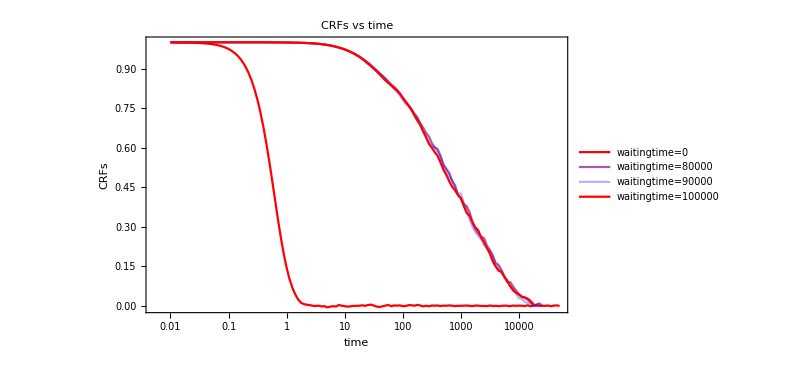

```mathematica
CRFswaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[t]],SISF[[1,wt,2,t]]},{t,Length[SISF[[1,wt,2]]]-10}],{wt,Length[wtlist]}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True,PlotStyle->redBluePlotConfig[3],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,Length[wtlist]}],PlotRange->All]
```

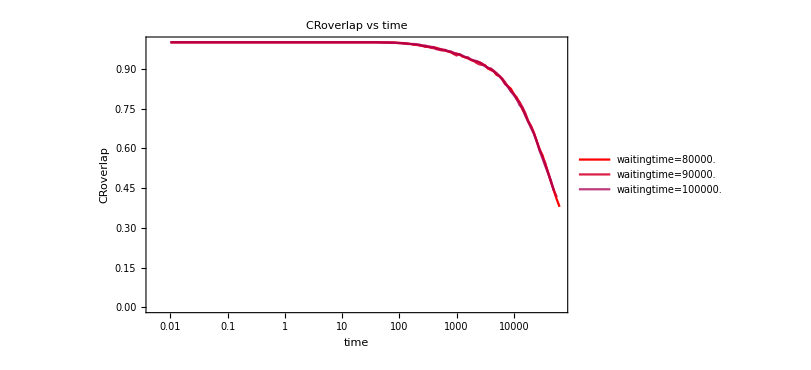

```mathematica
CRoverlapwaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[overlap[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]-5}],{wt,3}],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,3}],PlotRange->{All,{0,1}}]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
Length[Tlist]
```

26

```mathematica
SISF=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/SISFCRSISF_N4096_p3.9000_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,0}],{T,Length[Tlist]}];
```

```mathematica
CRSISFMean=Table[Table[SISF[[T,1,2,rec]],{rec,Length[SISF[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
testdata=Import[StringJoin["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p385/glassyDynamics_N4096_p3.8500_T",Tstring[[Length[Tlist]-8]],"_waitingTime",wtlistLongestString[[Length[Tlist]]],"_idx1.nc"],"Data"];time=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

```mathematica
fitCROverlapStartNum={4.545633497156052,6.972324797990245,7.688430481846143,9.342191365655887,11.359328382212755,15.816075884439703,17.103424454731552,21.189518319840886,23.81560922495133,27.8367722375015,30.685453336137705,33.82312067339929,36.55834456391838,39.51772229179588,41.89421685655501,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,80.,80.,80.,80.,80.,80.,80.,80.,80.,80.};
```

```mathematica
fitCROverlapStartPos=Table[Position[time,_?(#>fitCROverlapStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{45,48,49,51,53,55,56,58,59,60,61,62,63,63,64,65,65,65,65,65,65,70,70,70,70,70,70,70,70,70,70}

## CRSISF

```mathematica
SISF[[2,1]]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

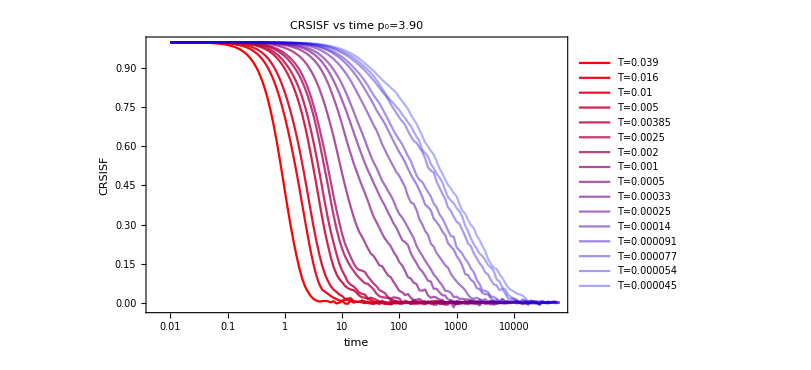

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],SISF[[T,1,2,rec]]},{rec,Length[SISF[[T,1,2]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time p_0=3.90",Joined->True]
```

```mathematica
fitCRSISFStartNum={3.54238575749071,5.17783361678472,7.85485320091976,11.6943383265391,13.6132971802572,20.6595265590617,26.4405800389533,37.9639814764309,63.4248910250324,92.785367817139,106.149064390338,170.646901855638,171.278227103386,207.059359528149,270.707606753432,276.007035267409,309.530362230405};
```

```mathematica
fitCRSISFStartPos=Table[Position[time,_?(#>fitCRSISFStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{42,46,49,53,54,58,60,63,68,71,72,76,76,78,80,80,81}

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISF[[T,1,2,rec]]]},{rec,fitCRSISFStartPos[[T]],Length[SISF[[T,1,2]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,1.0>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCRSISF
```

{FittedModel[0.0543372 ⅇ^(-1.24588 t^0.425351)],FittedModel[0.87842 ⅇ^(-1.39227 t^0.50706)],FittedModel[0.838863 ⅇ^(-0.823841 t^0.630111)],FittedModel[0.251039 ⅇ^(-0.147832 t^0.898693)],FittedModel[0.282493 ⅇ^(-0.131185 t^0.894367)],FittedModel[0.289412 ⅇ^(-0.0735491 t^0.89799)],FittedModel[0.815616 ⅇ^(-0.276237 t^0.607103)],FittedModel[0.393008 ⅇ^(-0.0318731 t^0.898826)],FittedModel[0.957344 ⅇ^(-0.133572 t^0.565906)],FittedModel[0.512864 ⅇ^(-0.0132858 t^0.850169)],FittedModel[0.800483 ⅇ^(-0.0428923 t^0.641664)],FittedModel[0.977679 ⅇ^(-0.0542188 t^0.555658)],FittedModel[0.740842 ⅇ^(-0.0159725 t^0.652972)],FittedModel[0.69562 ⅇ^(-0.00773381 t^0.723449)],FittedModel[0.912476 ⅇ^(-0.0206011 t^0.570977)],FittedModel[0.824488 ⅇ^(-0.0115329 t^0.618158)],FittedModel[0.883953 ⅇ^(-0.0143099 t^0.579519)]}

```mathematica
tauCRSISFfits=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{0.596396,0.520663,1.36006,8.39117,9.68952,18.2885,8.32344,46.2416,35.0693,161.19,135.321,189.719,564.239,829.48,897.484,1365.27,1522.57}

```mathematica
Length[TlistLongest]
```

0

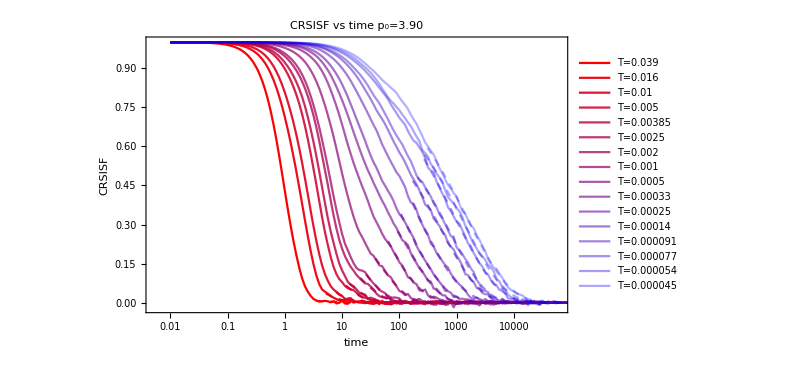

```mathematica
Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,fitCRSISFStartNum[[T]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRSISF_p380.jpeg",Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

Show::gcomb: Could not combine the graphics objects in Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,{}].

```mathematica
1/0.0002
```

5000.

#### Tau Alphas

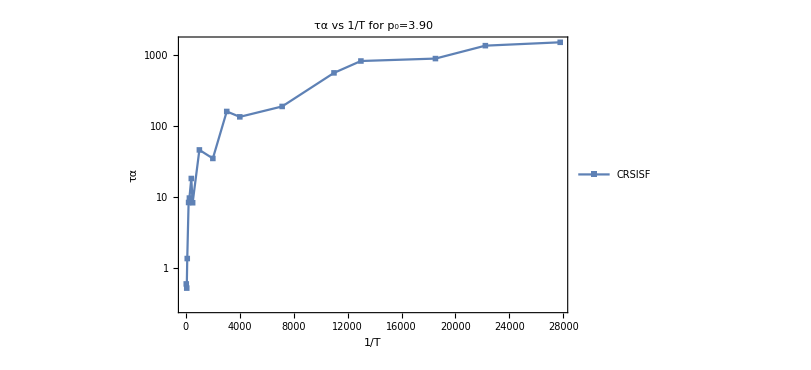

```mathematica
tauAlphafitingPlot=ListLogPlot[Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}],FrameLabel->{"1/T","τα"},PlotLegends->{"CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■"],Style["●"],Style["□"],Style["○"]},ImageSize->600,PlotLabel->"τα vs 1/T for p_0=3.90",Joined->True,PlotRange->All]
```

```mathematica
tauAlphaFitting=LinearModelFit[Table[{1/Tlist[[T]],Log10[tauCRSISFfits[[T]]]},{T,Length[Tlist]-3,Length[Tlist]}],{1,x},x]
```

FittedModel[2.64631+0.0000196844 x]

```mathematica
10^tauAlphaFitting[1/Tlist[[Length[Tlist]-1]]]
```

1212.67

```mathematica
Solve[tauAlphaFitting[1/T]==Log10[3000],T]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{T→0.000023693}}

```mathematica
Solve[tauAlphaFitting[1/T]==Log10[6000],T]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{T→0.0000173915}}

```mathematica
Solve[tauAlphaFitting[1/T]==Log10[8000],T]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{T→0.0000156626}}

```mathematica
Solve[tauAlphaFitting[1/T]==Log10[10000],T]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{T→0.0000145413}}